```mathematica
(*

atomic units

*)

ℏ=1;
m=1;
e=1;
```

10

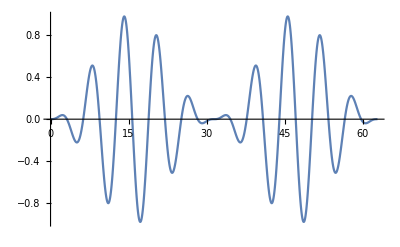

```mathematica
(* Recall *)
numberofcycles = 10
Plot[Sin[x/numberofcycles]^2*Sin[x],{x,0,10*2π}]
```

## Functions

```mathematica
(*

n and m times ω field mixing
modulated by sin(modw * t + modphase)

*)

Expand[ Sin[modphase+modw t]^2(1/(2*ⅈ)(EF1/Sqrt[1+epsilon1^2]*(x̂-ⅈ epsilon1 ŷ)ⅇ^(int1*ⅈ*w*t)+EF2/Sqrt[1+epsilon2^2]*(x̂-ⅈ epsilon2 ŷ)ⅇ^(int2*ⅈ w t))+1/(2*-ⅈ)(EF1/Sqrt[1+epsilon1^2]*(x̂+ⅈ epsilon1 ŷ)ⅇ^(-int1*ⅈ*w*t)+EF2/Sqrt[1+epsilon2^2]*(x̂+ⅈ epsilon2 ŷ)ⅇ^(-int2*ⅈ w t)))]
```

(ⅈ ⅇ^(-ⅈ int1 t w) EF1 x̂ Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))-(ⅈ ⅇ^(ⅈ int1 t w) EF1 x̂ Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))+(ⅈ ⅇ^(-ⅈ int2 t w) EF2 x̂ Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2))-(ⅈ ⅇ^(ⅈ int2 t w) EF2 x̂ Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2))-(ⅇ^(-ⅈ int1 t w) EF1 epsilon1 ŷ Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))-(ⅇ^(ⅈ int1 t w) EF1 epsilon1 ŷ Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))-(ⅇ^(-ⅈ int2 t w) EF2 epsilon2 ŷ Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2))-(ⅇ^(ⅈ int2 t w) EF2 epsilon2 ŷ Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2))

```mathematica
(*

electric field modulated as a pulse

*)

Ex[t_]=(ⅈ ⅇ^(-ⅈ int1 t w) EF1  Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))-(ⅈ ⅇ^(ⅈ int1 t w) EF1 Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))+(ⅈ ⅇ^(-ⅈ int2 t w) EF2  Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2))-(ⅈ ⅇ^(ⅈ int2 t w) EF2  Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2));
Ey[t_]=-(ⅇ^(-ⅈ int1 t w) EF1 epsilon1  Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))-(ⅇ^(ⅈ int1 t w) EF1 epsilon1  Sin[modphase+modw t]^2)/(2 √(1+epsilon1^2))-(ⅇ^(-ⅈ int2 t w) EF2 epsilon2  Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2))-(ⅇ^(ⅈ int2 t w) EF2 epsilon2 Sin[modphase+modw t]^2)/(2 √(1+epsilon2^2));
ef[t_]=({{Ex[t]}, {Ey[t]}});
```

```mathematica
(* 

vector potential 

A[t_]=Integrate[-ef[t],t];

*)

A[t_]={{(ⅈ (-1/(2 int1 int2 w)ⅈ ⅇ^(-ⅈ (int1+int2) t w) (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int1+ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1+ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int2+ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2)+(ⅈ ⅇ^(-ⅈ (int1+int2) t w) Cos[2 modw t] (-4 ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int1 modw^2 w Cos[2 modphase]-4 ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^2 w Cos[2 modphase]-4 ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int2 modw^2 w Cos[2 modphase]-4 ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^2 w Cos[2 modphase]+ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int1^2 int2 w^3 Cos[2 modphase]+ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 w^3 Cos[2 modphase]+ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int1 int2^2 w^3 Cos[2 modphase]+ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 w^3 Cos[2 modphase]-8 ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) modw^3 Sin[2 modphase]+8 ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^3 Sin[2 modphase]-8 ⅈ ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) modw^3 Sin[2 modphase]+8 ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^3 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int1^2 modw w^2 Sin[2 modphase]-2 ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw w^2 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int2^2 modw w^2 Sin[2 modphase]-2 ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw w^2 Sin[2 modphase]))/(2 (-2 modw+int1 w) (2 modw+int1 w) (-2 modw+int2 w) (2 modw+int2 w))+(ⅇ^(-ⅈ (int1+int2) t w) (8 ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) modw^3 Cos[2 modphase]-8 ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^3 Cos[2 modphase]+8 ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) modw^3 Cos[2 modphase]-8 ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^3 Cos[2 modphase]-2 ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int1^2 modw w^2 Cos[2 modphase]+2 ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw w^2 Cos[2 modphase]-2 ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int2^2 modw w^2 Cos[2 modphase]+2 ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw w^2 Cos[2 modphase]+4 ⅈ ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int1 modw^2 w Sin[2 modphase]+4 ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^2 w Sin[2 modphase]+4 ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int2 modw^2 w Sin[2 modphase]+4 ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^2 w Sin[2 modphase]-ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int1^2 int2 w^3 Sin[2 modphase]-ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 w^3 Sin[2 modphase]-ⅈ ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int1 int2^2 w^3 Sin[2 modphase]-ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 w^3 Sin[2 modphase]) Sin[2 modw t])/(2 (-2 modw+int1 w) (2 modw+int1 w) (-2 modw+int2 w) (2 modw+int2 w))))/(2 √(1+epsilon1^2) √(1+epsilon2^2))},{1/2 (-((ⅈ ⅇ^(ⅈ int1 t w+ⅈ int2 t w-ⅈ (int1+int2) t w) ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))) (-ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int1+ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1-ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int2+ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2))/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) int1 int2 w))-(ⅈ ⅇ^(ⅈ int1 t w+ⅈ int2 t w-ⅈ (int1+int2) t w) ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))) Cos[2 modw t] (-4 ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^2 w Cos[2 modphase]+4 ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^2 w Cos[2 modphase]-4 ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^2 w Cos[2 modphase]+4 ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^2 w Cos[2 modphase]+ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 w^3 Cos[2 modphase]-ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 w^3 Cos[2 modphase]+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 w^3 Cos[2 modphase]-ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 w^3 Cos[2 modphase]-8 ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 modw^3 Sin[2 modphase]-8 ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^3 Sin[2 modphase]-8 ⅈ ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) modw^3 Sin[2 modphase]-8 ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^3 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw w^2 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw w^2 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw w^2 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw w^2 Sin[2 modphase]))/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) (-2 modw+int1 w) (2 modw+int1 w) (-2 modw+int2 w) (2 modw+int2 w))+(ⅇ^(ⅈ int1 t w+ⅈ int2 t w-ⅈ (int1+int2) t w) ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))) (-8 ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 modw^3 Cos[2 modphase]-8 ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^3 Cos[2 modphase]-8 ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) modw^3 Cos[2 modphase]-8 ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^3 Cos[2 modphase]+2 ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw w^2 Cos[2 modphase]+2 ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw w^2 Cos[2 modphase]+2 ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw w^2 Cos[2 modphase]+2 ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw w^2 Cos[2 modphase]-4 ⅈ ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^2 w Sin[2 modphase]+4 ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^2 w Sin[2 modphase]-4 ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^2 w Sin[2 modphase]+4 ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^2 w Sin[2 modphase]+ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 w^3 Sin[2 modphase]-ⅈ ⅇ^(ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 w^3 Sin[2 modphase]+ⅈ ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 w^3 Sin[2 modphase]-ⅈ ⅇ^(ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 w^3 Sin[2 modphase]) Sin[2 modw t])/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) (-2 modw+int1 w) (2 modw+int1 w) (-2 modw+int2 w) (2 modw+int2 w)))}};
```

```mathematica
(* 


quiver motion

alpha[t_]=Integrate[A[t],t];

*)

alpha[t_]={{(ⅈ (-(ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2))/(2 int1^2 w^2)-(ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2))/(2 int2^2 w^2)-(ⅈ ⅇ^(-ⅈ (int1+int2) t w) ((ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) int1)/(int2 w)+(ⅈ ⅇ^(ⅈ int2 t w) EF1 √(1+epsilon2^2) int2)/(int1 w)))/(2 int1 int2 w)+(ⅈ (-1/2 ⅈ Cos[2 modw t]-1/2 Sin[2 modw t]) (32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]+8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase]+8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]-ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase]+ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase]-ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase]+ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase-4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase-4 modw t]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]-1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]-1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase+4 modw t]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]+4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]+4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]-1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]-1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]+64 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase]-64 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase]+64 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase]-64 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]+4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase]+4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]+4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]+4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]-1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]-1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]))/(2 (2 modw-int1 w) (-2 modw+int1 w) (2 modw+int1 w)^2 (2 modw-int2 w) (-2 modw+int2 w) (2 modw+int2 w)^2)+((1/2 Cos[2 modw t]-1/2 ⅈ Sin[2 modw t]) (-64 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase]+64 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase]-64 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase]+64 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]-4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase]-4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase-4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase-4 modw t]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]+1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]-1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]+1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]-1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Cos[2 modphase+4 modw t]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]+4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]+4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]-1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]-1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]-8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase]-8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]+ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase]-ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase]+ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase]-ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) modw^6 Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2 modw^5 w Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]+4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]+4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]-1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]-1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]))/(2 (2 modw-int1 w) (-2 modw+int1 w) (2 modw+int1 w)^2 (2 modw-int2 w) (-2 modw+int2 w) (2 modw+int2 w)^2)))/(2 √(1+epsilon1^2) √(1+epsilon2^2))},{1/2 (-((ⅇ^(ⅈ int1 t w+ⅈ int2 t w-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))))/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) int1^2 w^2))-(ⅇ^(ⅈ int1 t w+ⅈ int2 t w-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))))/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) int2^2 w^2)-(ⅈ ⅇ^(ⅈ int1 t w+ⅈ int2 t w-ⅈ (int1+int2) t w) ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))) (-(ⅈ ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2 int1)/(int2 w)-(ⅈ ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2) int2)/(int1 w)))/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) int1 int2 w)-(ⅈ ⅇ^(ⅈ int1 t w+ⅈ int2 t w) ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))) (1/2 ⅈ Cos[2 modw t]+1/2 Sin[2 modw t]) (-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]-8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase]-8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]+ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase]+ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase]+ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase]+ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase-4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase-4 modw t]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]+1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]+1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]+1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]-64 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase]-64 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase]-64 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase]-64 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]-4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase]-4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]-1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]))/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) (-2 modw+int1 w)^2 (2 modw+int1 w)^2 (-2 modw+int2 w)^2 (2 modw+int2 w)^2)+(ⅇ^(ⅈ int1 t w+ⅈ int2 t w) ((ⅇ^(-ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(ⅈ int1 t w) EF1 epsilon1)/(√(1+epsilon1^2))+(ⅇ^(-ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))+(ⅇ^(ⅈ int2 t w) EF2 epsilon2)/(√(1+epsilon2^2))) (1/2 Cos[2 modw t]-1/2 ⅈ Sin[2 modw t]) (64 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase]+64 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase]+64 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase]+64 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase]-32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase]-32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase]+16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase]+16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase]+4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase]+4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase]-2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase]-2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase-4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase-4 modw t]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase-4 modw t]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase-4 modw t]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase-4 modw t]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase-4 modw t]-1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]-1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase-4 modw t]-1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]-1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase-4 modw t]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Cos[2 modphase+4 modw t]+32 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Cos[2 modphase+4 modw t]+32 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase+4 modw t]-32 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]+8 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Cos[2 modphase+4 modw t]-16 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]+16 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]-4 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Cos[2 modphase+4 modw t]+2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]-2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Cos[2 modphase+4 modw t]+1/2 ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]+1/2 ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Cos[2 modphase+4 modw t]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase]+8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase]+8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase]-ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase]-ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase]-ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase]-ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase]-32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase-4 modw t]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) modw^6 Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 modw^5 w Sin[2 modphase+4 modw t]+32 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase+4 modw t]-32 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2 modw^5 w Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]+8 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^2 modw^4 w^2 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2 modw^3 w^3 Sin[2 modphase+4 modw t]-16 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]+16 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^2 modw^3 w^3 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]-4 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^2 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int2^4 modw^2 w^4 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2 modw w^5 Sin[2 modphase+4 modw t]+2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]-2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1 int2^4 modw w^5 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(ⅈ int1 t w-ⅈ (int1+int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (int1+2 int2) t w) EF2 √(1+epsilon1^2) epsilon2 int1^4 int2^2 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(ⅈ int2 t w-ⅈ (int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]+1/2 ⅈ ⅇ^(-ⅈ (int1+int2) t w+ⅈ (2 int1+int2) t w) EF1 epsilon1 √(1+epsilon2^2) int1^2 int2^4 w^6 Sin[2 modphase+4 modw t]))/(2 (ⅇ^(ⅈ int1 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int1 t w+2 ⅈ int2 t w) EF2 √(1+epsilon1^2) epsilon2+ⅇ^(ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)+ⅇ^(2 ⅈ int1 t w+ⅈ int2 t w) EF1 epsilon1 √(1+epsilon2^2)) (-2 modw+int1 w)^2 (2 modw+int1 w)^2 (-2 modw+int2 w)^2 (2 modw+int2 w)^2))}};
```

## Milosevic Eqns

```mathematica
(*

eqn (19) milosevic
aka saddle point finder eqn w/ fixed real tf

*)

1/(2m)*Transpose[(m/tau*(alpha[tf-tau]-alpha[tf])+e*A[tf-tau])].(m/tau*(alpha[tf-tau]-alpha[tf])+e*A[tf-tau])-gse//InputForm
```

{
 {
  -gse + 
   ((((I/2)*(((-I/2)*(E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1 + 
             E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1 + 
             E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2 + 
             E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2))/
           (E^(I*(int1 + int2)*(-tau + tf)*w)*int1*int2*w) + 
          ((I/2)*Cos[2*modw*(-tau + tf)]*(-4*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int1*modw^2*w*Cos[2*modphase] - 4*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1*modw^2*w*Cos[2*modphase] - 4*E^(I*int1*(-tau + tf)*w)*
              EF2*Sqrt[1 + epsilon1^2]*int2*modw^2*w*Cos[2*modphase] - 
             4*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^2*w*
              Cos[2*modphase] + E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*
              w^3*Cos[2*modphase] + E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*Cos[2*modphase] + E^(I*int2*(-tau + tf)*w)*
              EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Cos[2*modphase] + 
             E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*
              Cos[2*modphase] - (8*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*
              Sin[2*modphase] + (8*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*modw^3*Sin[2*modphase] - (8*I)*E^(I*int2*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*modw^3*Sin[2*modphase] + (8*I)*E^(I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^3*Sin[2*modphase] + 
             (2*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw*w^2*
              Sin[2*modphase] - (2*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*int1^2*modw*w^2*Sin[2*modphase] + 
             (2*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*
              Sin[2*modphase] - (2*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*Sin[2*modphase]))/
           (E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*(2*modw + int1*w)*
            (-2*modw + int2*w)*(2*modw + int2*w)) + 
          ((8*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*Cos[2*modphase] - 
             8*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*
              Cos[2*modphase] + 8*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^3*
              Cos[2*modphase] - 8*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              modw^3*Cos[2*modphase] - 2*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
              int1^2*modw*w^2*Cos[2*modphase] + 2*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*int1^2*modw*w^2*Cos[2*modphase] - 
             2*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*
              Cos[2*modphase] + 2*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int2^2*modw*w^2*Cos[2*modphase] + (4*I)*E^(I*int2*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1*modw^2*w*Sin[2*modphase] + 
             (4*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^2*w*
              Sin[2*modphase] + (4*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*
              modw^2*w*Sin[2*modphase] + (4*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*int2*modw^2*w*Sin[2*modphase] - I*E^(I*int1*(-tau + tf)*w)*
              EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*Sin[2*modphase] - 
             I*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*
              Sin[2*modphase] - I*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*
              int2^2*w^3*Sin[2*modphase] - I*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Sin[2*modphase])*Sin[2*modw*(-tau + tf)])/
           (2*E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*(2*modw + int1*w)*
            (-2*modw + int2*w)*(2*modw + int2*w))))/(Sqrt[1 + epsilon1^2]*
         Sqrt[1 + epsilon2^2]) + 
       (((-I/2)*(-(E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[
                1 + epsilon2^2])/(2*int1^2*w^2) - (E^((-I)*(int1 + int2)*tf*w + 
                I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2])/(2*int2^2*w^2) - 
            ((I/2)*((I*E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1)/(int2*w) + 
               (I*E^(I*int2*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2)/(int1*w)))/
             (E^(I*(int1 + int2)*tf*w)*int1*int2*w) + ((I/2)*((-I/2)*Cos[2*modw*tf] - 
               Sin[2*modw*tf]/2)*(32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 32*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*modw^5*w*Cos[2*modphase] + 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 32*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2*modw^5*w*Cos[2*modphase] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 16*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*modw^4*w^2*Cos[2*modphase] - 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase] + 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Cos[2*modphase] - 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 16*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^2*modw^3*w^3*Cos[2*modphase] + 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 8*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 8*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 8*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 2*E^(I*int1*tf*w - I*(int1 + int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 2*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2*modw*w^5*Cos[2*modphase] + 2*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 2*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^4*modw*w^5*Cos[2*modphase] - E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase] + 
               E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2^2*w^6*Cos[2*modphase] - E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] + 
               E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^4*w^6*Cos[2*modphase] + 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*tf] - 32*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Cos[2*modphase - 4*modw*tf] + 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*tf] - 32*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Cos[2*modphase - 4*modw*tf] - 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 8*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Cos[2*modphase - 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 
                  4*modw*tf] - 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 8*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 16*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase - 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase - 4*modw*tf] + 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 2*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 4*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase - 4*modw*tf] - 4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase - 4*modw*tf] + 4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 4*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 2*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Cos[2*modphase - 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase - 4*modw*tf] - (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                 Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/2 + 
               (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                 int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/2 - 
               (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
                 w^6*Cos[2*modphase - 4*modw*tf])/2 + (E^((-I)*(int1 + int2)*tf*w + 
                   I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                 Cos[2*modphase - 4*modw*tf])/2 - 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 32*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 32*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*tf] - 32*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*modw^5*w*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Cos[2*modphase + 4*modw*tf] - 32*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Cos[2*modphase + 4*modw*tf] + 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 8*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Cos[2*modphase + 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 
                  4*modw*tf] - 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 8*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 16*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase + 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase + 4*modw*tf] + 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 16*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
                Cos[2*modphase + 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
                Cos[2*modphase + 4*modw*tf] - 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 2*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 4*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase + 4*modw*tf] - 4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase + 4*modw*tf] + 4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 4*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 2*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Cos[2*modphase + 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase + 4*modw*tf] - 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase + 4*modw*tf] - 2*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2*modw*w^5*Cos[2*modphase + 4*modw*tf] - 2*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Cos[2*modphase + 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase + 
                  4*modw*tf] - (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                 Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/2 + 
               (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                 int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/2 - 
               (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
                 w^6*Cos[2*modphase + 4*modw*tf])/2 + (E^((-I)*(int1 + int2)*tf*w + 
                   I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                 Cos[2*modphase + 4*modw*tf])/2 + (64*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase] - (64*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Sin[2*modphase] + (64*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase] - (64*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Sin[2*modphase] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*modw^5*w*Sin[2*modphase] - (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2*modw^5*w*Sin[2*modphase] - (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*modw^4*w^2*Sin[2*modphase] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int2^2*modw^4*w^2*Sin[2*modphase] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
                Sin[2*modphase] + (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + (4*I)*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*
                w^4*Sin[2*modphase] - (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase] + (4*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Sin[2*modphase] - (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase] - (2*I)*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*
                modw*w^5*Sin[2*modphase] - (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
                Sin[2*modphase] - (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - (2*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^4*modw*w^5*Sin[2*modphase] - (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*tf] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Sin[2*modphase - 4*modw*tf] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*tf] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Sin[2*modphase - 4*modw*tf] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 
                  4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] + (8*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
                w^2*Sin[2*modphase - 4*modw*tf] - (8*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*tf] + (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - (8*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] + (16*I)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*tf] - (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + (2*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] - (4*I)*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Sin[2*modphase - 4*modw*tf] + (4*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Sin[2*modphase - 4*modw*tf] - (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + 
               (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*tf] - 
               (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*
                modw^2*w^4*Sin[2*modphase - 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Sin[2*modphase - 4*modw*tf] + (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*tf] - (I/2)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*tf] + (I/2)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase - 4*modw*tf] - (I/2)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase - 4*modw*tf] - (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase + 4*modw*tf] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Sin[2*modphase + 4*modw*tf] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*tf] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Sin[2*modphase + 4*modw*tf] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*tf] - 
               (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*tf] - (32*I)*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Sin[2*modphase + 4*modw*tf] - (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Sin[2*modphase + 4*modw*tf] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - 
               (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - (8*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
                w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*tf] - (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + (16*I)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*tf] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + 
               (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + 
               (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*
                int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + (16*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*
                w^4*Sin[2*modphase + 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
                Sin[2*modphase + 4*modw*tf] + (4*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - 
               (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] + 
               (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*
                int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - (4*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Sin[2*modphase + 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Sin[2*modphase + 4*modw*tf] - (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*
                modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Sin[2*modphase + 4*modw*tf] - (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*tf] + (I/2)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*tf] - (I/2)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase + 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase + 4*modw*tf]))/((2*modw - int1*w)*(-2*modw + int1*w)*
              (2*modw + int1*w)^2*(2*modw - int2*w)*(-2*modw + int2*w)*(2*modw + int2*w)^2) + 
            ((Cos[2*modw*tf]/2 - (I/2)*Sin[2*modw*tf])*(-64*E^(I*int1*tf*w - I*(int1 + int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase] + 64*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Cos[2*modphase] - 64*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase] + 64*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase] + 32*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
                Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 32*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 32*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
                Cos[2*modphase] - 32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 32*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*
                w^2*Cos[2*modphase] - 32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 16*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*
                modw^3*w^3*Cos[2*modphase] - 16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
                modw^3*w^3*Cos[2*modphase] - 16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 4*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*
                w^4*Cos[2*modphase] + 4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase] - 4*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Cos[2*modphase] + 4*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase] + 2*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*
                modw*w^5*Cos[2*modphase] + 2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 2*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*
                modw*w^5*Cos[2*modphase] + 2*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] - 32*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
                Cos[2*modphase - 4*modw*tf] + 32*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
                Cos[2*modphase - 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*tf] + 32*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Cos[2*modphase - 4*modw*tf] + 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 8*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Cos[2*modphase - 4*modw*tf] - 8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 
                  4*modw*tf] + 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 8*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 16*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase - 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase - 4*modw*tf] - 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 2*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 4*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase - 4*modw*tf] + 4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase - 4*modw*tf] - 4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 4*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 2*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Cos[2*modphase - 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase - 4*modw*tf] + (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                 Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/2 - 
               (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                 int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/2 + 
               (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
                 w^6*Cos[2*modphase - 4*modw*tf])/2 - (E^((-I)*(int1 + int2)*tf*w + 
                   I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                 Cos[2*modphase - 4*modw*tf])/2 - 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 32*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 32*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*tf] - 32*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*modw^5*w*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Cos[2*modphase + 4*modw*tf] - 32*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Cos[2*modphase + 4*modw*tf] + 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 8*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Cos[2*modphase + 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 
                  4*modw*tf] - 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 8*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 16*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase + 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Cos[2*modphase + 4*modw*tf] + 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 16*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 16*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
                Cos[2*modphase + 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
                Cos[2*modphase + 4*modw*tf] - 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 2*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 4*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase + 4*modw*tf] - 4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Cos[2*modphase + 4*modw*tf] + 4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 4*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 2*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Cos[2*modphase + 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase + 4*modw*tf] - 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase + 4*modw*tf] - 2*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2*modw*w^5*Cos[2*modphase + 4*modw*tf] - 2*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Cos[2*modphase + 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase + 
                  4*modw*tf] - (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                 Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/2 + 
               (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                 int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/2 - 
               (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
                 w^6*Cos[2*modphase + 4*modw*tf])/2 + (E^((-I)*(int1 + int2)*tf*w + 
                   I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                 Cos[2*modphase + 4*modw*tf])/2 - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*modw^5*w*Sin[2*modphase] - (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2*modw^5*w*Sin[2*modphase] + (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase] - (16*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*modw^4*w^2*Sin[2*modphase] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase] - (16*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Sin[2*modphase] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
                Sin[2*modphase] + (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] - (8*I)*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase] + (8*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Sin[2*modphase] - (8*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + (8*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Sin[2*modphase] - (2*I)*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
                Sin[2*modphase] - (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - (2*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*
                modw*w^5*Sin[2*modphase] - (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Sin[2*modphase] + I*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase] - I*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2^2*w^6*Sin[2*modphase] + I*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
                EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase] - I*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^4*w^6*Sin[2*modphase] + (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                   w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*tf] - (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Sin[2*modphase - 4*modw*tf] + (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*tf] - (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Sin[2*modphase - 4*modw*tf] - (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*
                   tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 
                  4*modw*tf] + (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - (8*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
                w^2*Sin[2*modphase - 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*tf] - (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] + (8*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - (16*I)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*tf] + (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*tf] + (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] - (2*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + (4*I)*E^(I*int1*tf*w - 
                  I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Sin[2*modphase - 4*modw*tf] - (4*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
                Sin[2*modphase - 4*modw*tf] + (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*tf] - 
               (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + 
               (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*
                modw^2*w^4*Sin[2*modphase - 4*modw*tf] - (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Sin[2*modphase - 4*modw*tf] - (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*tf] + (I/2)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*tf] - (I/2)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase - 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase - 4*modw*tf] - (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase + 4*modw*tf] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Sin[2*modphase + 4*modw*tf] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*tf] + (32*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Sin[2*modphase + 4*modw*tf] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*
                   tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*tf] - 
               (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*tf] - (32*I)*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Sin[2*modphase + 4*modw*tf] - (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
                Sin[2*modphase + 4*modw*tf] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - 
               (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - (8*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
                w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*tf] - (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + (16*I)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*tf] + (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + 
               (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + 
               (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*
                int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + (16*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*
                w^4*Sin[2*modphase + 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
                Sin[2*modphase + 4*modw*tf] + (4*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - 
               (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] + 
               (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*
                int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - (4*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*
                w^4*Sin[2*modphase + 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Sin[2*modphase + 4*modw*tf] - (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*
                E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*
                modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Sin[2*modphase + 4*modw*tf] - (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*tf] + (I/2)*
                E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*tf] - (I/2)*E^(I*int2*tf*w - 
                  I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase + 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase + 4*modw*tf]))/(2*(2*modw - int1*w)*(-2*modw + int1*w)*
              (2*modw + int1*w)^2*(2*modw - int2*w)*(-2*modw + int2*w)*(2*modw + int2*w)^2)))/
          (Sqrt[1 + epsilon1^2]*Sqrt[1 + epsilon2^2]) + 
         ((I/2)*(-(E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               Sqrt[1 + epsilon2^2])/(2*int1^2*w^2) - (E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2])/(2*int2^2*w^2) - 
            ((I/2)*((I*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1)/(int2*w) + 
               (I*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2)/(int1*w)))/
             (E^(I*(int1 + int2)*(-tau + tf)*w)*int1*int2*w) + 
            ((I/2)*((-I/2)*Cos[2*modw*(-tau + tf)] - Sin[2*modw*(-tau + tf)]/2)*
              (32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 32*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] - 16*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 16*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] - 16*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase] + 16*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 16*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 16*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] + 8*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 8*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 8*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 8*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 2*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 2*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 2*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 2*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] - 
               E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase] + 
               E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase] - 
               E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] + 
               E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] + 32*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 32*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 16*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 
                  4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
                w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 2*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase - 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase - 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                   I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
                 Cos[2*modphase - 4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*
                    w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*
                 int2^2*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/2 - 
               (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                 Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/
                2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                 EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*
                    (-tau + tf)])/2 - 32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 16*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase + 
                  4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*
                w^3*Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*
                w^3*Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^2*modw^3*w^3*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 
                  4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
                w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
                Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*
                w^5*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*
                w^5*Cos[2*modphase + 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                   I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
                 Cos[2*modphase + 4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*
                    w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*
                 int2^2*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/2 - 
               (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                 Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/
                2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                 EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*
                    (-tau + tf)])/2 + (64*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*
                   (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase] - (64*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase] + (64*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
                Sin[2*modphase] - (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
                Sin[2*modphase] - (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - (32*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - (32*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase] + (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase] - (32*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase] + (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase] + (16*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + (4*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase] - (4*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase] + (4*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase] - (4*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase] - (2*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - (2*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - (2*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - (2*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - (32*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + (16*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
               (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*
                   (-tau + tf)] + (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 
                  4*modw*(-tau + tf)] - (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*(-tau + tf)] + (8*I)*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*(-tau + tf)] - (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
                w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*(-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - (2*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*
                   (-tau + tf)] - (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 
                  4*modw*(-tau + tf)] + (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - (4*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 
                  4*modw*(-tau + tf)] + (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - (2*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*
                   (-tau + tf)] + (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 
                  4*modw*(-tau + tf)] - (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
                Sin[2*modphase - 4*modw*(-tau + tf)] + (I/2)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase - 4*modw*(-tau + tf)] - (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
                w^6*Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
                Sin[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
                Sin[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
               (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
               (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*
                   (-tau + tf)] - (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 
                  4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (8*I)*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
                w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 
                  4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*
                w^3*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*
                w^3*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*
                   (-tau + tf)] + (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 
                  4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 
                  4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*
                   (-tau + tf)] - (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 
                  4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*
                w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*
                modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - (I/2)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*
                   (-tau + tf)] - (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 
                  4*modw*(-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase + 4*modw*(-tau + tf)]))/((2*modw - int1*w)*(-2*modw + int1*w)*
              (2*modw + int1*w)^2*(2*modw - int2*w)*(-2*modw + int2*w)*(2*modw + int2*w)^2) + 
            ((Cos[2*modw*(-tau + tf)]/2 - (I/2)*Sin[2*modw*(-tau + tf)])*
              (-64*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase] + 64*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Cos[2*modphase] - 64*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*
                   (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase] + 64*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase] + 32*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
                Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                   (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 32*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 32*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 32*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 16*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 16*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 4*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase] + 4*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase] - 4*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase] + 4*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase] + 2*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 2*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 2*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 2*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] - 32*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 32*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 16*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
               2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
               4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 
                  4*modw*(-tau + tf)] + 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 4*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
                w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 4*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase - 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase - 4*modw*(-tau + tf)] + (E^(I*int1*(-tau + tf)*w - 
                   I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
                 Cos[2*modphase - 4*modw*(-tau + tf)])/2 - (E^((-I)*(int1 + int2)*(-tau + tf)*
                    w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*
                 int2^2*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/2 + 
               (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                 Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/
                2 - (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                 EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*
                    (-tau + tf)])/2 - 32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 16*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
               16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase + 
                  4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*
                w^3*Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*
                w^3*Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^2*modw^3*w^3*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 
               4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 
                  4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
                w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
                Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
                Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*
                w^5*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*
                w^5*Cos[2*modphase + 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                   I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
                 Cos[2*modphase + 4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*
                    w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*
                 int2^2*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/2 - 
               (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                 Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/
                2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                 EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*
                    (-tau + tf)])/2 - (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*
                   (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - 
               (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - (32*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] + (16*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase] - (16*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase] + (16*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase] - (16*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase] + (16*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + (16*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] - (8*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + (8*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] - (8*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + (8*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] - (2*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - (2*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - (2*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - (2*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] + I*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase] - I*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase] + I*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase] - I*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase] + (32*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + (32*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*
                E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - (16*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
               (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*
                   (-tau + tf)] - (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 
                  4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*(-tau + tf)] - (8*I)*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
                w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - (16*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase - 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + (2*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*
                   (-tau + tf)] + (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 
                  4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + (4*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 
                  4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + (2*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*
                   (-tau + tf)] - (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 
                  4*modw*(-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
                Sin[2*modphase - 4*modw*(-tau + tf)] - (I/2)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase - 4*modw*(-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
                w^6*Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
                Sin[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
                modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
                Sin[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
               (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
               (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*
                   (-tau + tf)] - (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 
                  4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (8*I)*E^(I*int1*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
                w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 
                  4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*
                w^3*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*
                w^3*Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*
                   (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
                int1*int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*
                   (-tau + tf)] + (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 
                  4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 
                  4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
                modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*
                E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
                Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*
                EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*
                   (-tau + tf)] - (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 
                  4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*
                w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^(I*int2*(-tau + tf)*w - 
                  I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
                Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*
                modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - (I/2)*
                E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
               (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*
                EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*
                   (-tau + tf)] - (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 
                  4*modw*(-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Sin[2*modphase + 4*modw*(-tau + tf)]))/(2*(2*modw - int1*w)*(-2*modw + int1*w)*
              (2*modw + int1*w)^2*(2*modw - int2*w)*(-2*modw + int2*w)*(2*modw + int2*w)^2)))/
          (Sqrt[1 + epsilon1^2]*Sqrt[1 + epsilon2^2]))/tau)^2 + 
     ((((-I/2)*E^(I*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
           ((EF1*epsilon1)/(E^(I*int1*(-tau + tf)*w)*Sqrt[1 + epsilon1^2]) + 
            (E^(I*int1*(-tau + tf)*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + 
            (EF2*epsilon2)/(E^(I*int2*(-tau + tf)*w)*Sqrt[1 + epsilon2^2]) + 
            (E^(I*int2*(-tau + tf)*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2])*
           (-(E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1) + 
            E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1 - 
            E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2 + 
            E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2))/
          ((E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + 
            E^(I*int1*(-tau + tf)*w + (2*I)*int2*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2 + E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + 
            E^((2*I)*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2])*int1*int2*w) - 
         ((I/2)*E^(I*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
              w)*((EF1*epsilon1)/(E^(I*int1*(-tau + tf)*w)*Sqrt[1 + epsilon1^2]) + 
            (E^(I*int1*(-tau + tf)*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + 
            (EF2*epsilon2)/(E^(I*int2*(-tau + tf)*w)*Sqrt[1 + epsilon2^2]) + 
            (E^(I*int2*(-tau + tf)*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2])*
           Cos[2*modw*(-tau + tf)]*(-4*E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2]*int1*modw^2*w*Cos[2*modphase] + 
            4*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
             modw^2*w*Cos[2*modphase] - 4*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2*int2*modw^2*w*Cos[2*modphase] + 4*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^2*w*Cos[2*modphase] + 
            E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*w^3*
             Cos[2*modphase] - E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2*int1^2*int2*w^3*Cos[2*modphase] + E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Cos[2*modphase] - 
            E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             w^3*Cos[2*modphase] - (8*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2*modw^3*Sin[2*modphase] - (8*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*epsilon2*modw^3*Sin[2*modphase] - 
            (8*I)*E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^3*
             Sin[2*modphase] - (8*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2]*modw^3*Sin[2*modphase] + (2*I)*E^(I*int1*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw*w^2*Sin[2*modphase] + 
            (2*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*
             modw*w^2*Sin[2*modphase] + (2*I)*E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*Sin[2*modphase] + 
            (2*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^2*
             modw*w^2*Sin[2*modphase]))/((E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2 + E^(I*int1*(-tau + tf)*w + (2*I)*int2*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*epsilon2 + E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2] + E^((2*I)*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w)*EF1*
             epsilon1*Sqrt[1 + epsilon2^2])*(-2*modw + int1*w)*(2*modw + int1*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)) + 
         (E^(I*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
           ((EF1*epsilon1)/(E^(I*int1*(-tau + tf)*w)*Sqrt[1 + epsilon1^2]) + 
            (E^(I*int1*(-tau + tf)*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + 
            (EF2*epsilon2)/(E^(I*int2*(-tau + tf)*w)*Sqrt[1 + epsilon2^2]) + 
            (E^(I*int2*(-tau + tf)*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2])*
           (-8*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^3*
             Cos[2*modphase] - 8*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2*modw^3*Cos[2*modphase] - 8*E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2]*modw^3*Cos[2*modphase] - 
            8*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^3*
             Cos[2*modphase] + 2*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
             int1^2*modw*w^2*Cos[2*modphase] + 2*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw*w^2*Cos[2*modphase] + 
            2*E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*
             Cos[2*modphase] + 2*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*Cos[2*modphase] - 
            (4*I)*E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^2*w*
             Sin[2*modphase] + (4*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2]*int1*modw^2*w*Sin[2*modphase] - 
            (4*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^2*w*
             Sin[2*modphase] + (4*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^2*w*Sin[2*modphase] + 
            I*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*w^3*
             Sin[2*modphase] - I*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2*int1^2*int2*w^3*Sin[2*modphase] + I*E^(I*int2*(-tau + tf)*w)*EF1*
             epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Sin[2*modphase] - 
            I*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
             int2^2*w^3*Sin[2*modphase])*Sin[2*modw*(-tau + tf)])/
          (2*(E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + 
            E^(I*int1*(-tau + tf)*w + (2*I)*int2*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             epsilon2 + E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + 
            E^((2*I)*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w)*EF1*epsilon1*
             Sqrt[1 + epsilon2^2])*(-2*modw + int1*w)*(2*modw + int1*w)*(-2*modw + int2*w)*
           (2*modw + int2*w)))/2 + 
       (((E^(I*int1*tf*w + I*int2*tf*w - I*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
             epsilon1*Sqrt[1 + epsilon2^2]*((EF1*epsilon1)/(E^(I*int1*tf*w)*
                Sqrt[1 + epsilon1^2]) + (E^(I*int1*tf*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + 
              (EF2*epsilon2)/(E^(I*int2*tf*w)*Sqrt[1 + epsilon2^2]) + (E^(I*int2*tf*w)*EF2*
                epsilon2)/Sqrt[1 + epsilon2^2]))/(2*(E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int1*tf*w + (2*I)*int2*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + 
              E^((2*I)*int1*tf*w + I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2])*int1^2*
             w^2) + (E^(I*int1*tf*w + I*int2*tf*w - I*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*((EF1*epsilon1)/(E^(I*int1*tf*w)*
                Sqrt[1 + epsilon1^2]) + (E^(I*int1*tf*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + 
              (EF2*epsilon2)/(E^(I*int2*tf*w)*Sqrt[1 + epsilon2^2]) + (E^(I*int2*tf*w)*EF2*
                epsilon2)/Sqrt[1 + epsilon2^2]))/(2*(E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int1*tf*w + (2*I)*int2*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + 
              E^((2*I)*int1*tf*w + I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2])*int2^2*
             w^2) + ((I/2)*E^(I*int1*tf*w + I*int2*tf*w - I*(int1 + int2)*tf*w)*
             ((EF1*epsilon1)/(E^(I*int1*tf*w)*Sqrt[1 + epsilon1^2]) + (E^(I*int1*tf*w)*EF1*
                epsilon1)/Sqrt[1 + epsilon1^2] + (EF2*epsilon2)/(E^(I*int2*tf*w)*
                Sqrt[1 + epsilon2^2]) + (E^(I*int2*tf*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2])*
             (((-I)*E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1)/(int2*w) - 
              (I*E^(I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2)/(int1*w)))/
            ((E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + E^(I*int1*tf*w + 
                 (2*I)*int2*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + E^(I*int2*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2] + E^((2*I)*int1*tf*w + I*int2*tf*w)*EF1*epsilon1*
               Sqrt[1 + epsilon2^2])*int1*int2*w) + ((I/2)*E^(I*int1*tf*w + I*int2*tf*w)*
             ((EF1*epsilon1)/(E^(I*int1*tf*w)*Sqrt[1 + epsilon1^2]) + (E^(I*int1*tf*w)*EF1*
                epsilon1)/Sqrt[1 + epsilon1^2] + (EF2*epsilon2)/(E^(I*int2*tf*w)*
                Sqrt[1 + epsilon2^2]) + (E^(I*int2*tf*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2])*
             ((I/2)*Cos[2*modw*tf] + Sin[2*modw*tf]/2)*(-32*E^(I*int2*tf*w - I*(int1 + int2)*
                  tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] - 32*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[
                2*modphase] + 32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[2*modphase] + 
              16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^
                2*modw^4*w^2*Cos[2*modphase] + 16*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^
                2*Cos[2*modphase] + 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Cos[2*modphase] + 
              16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int2^2*modw^4*w^2*Cos[2*modphase] + 16*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^
                3*Cos[2*modphase] - 16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^3*Cos[2*modphase] + 
              16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
               int2^2*modw^3*w^3*Cos[2*modphase] - 16*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^
                3*w^3*Cos[2*modphase] - 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              8*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 8*E^(I*int2*tf*w - 
                 I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^
                2*w^4*Cos[2*modphase] - 8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*
               EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*int2*modw*w^5*Cos[2*modphase] + 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^
                5*Cos[2*modphase] - 2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 
              2*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 
              E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*int2^2*w^6*Cos[2*modphase] + E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase] + 
              E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^
                2*int2^4*w^6*Cos[2*modphase] + E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                  tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] - 
              32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^
                6*Cos[2*modphase - 4*modw*tf] - 32*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Cos[
                2*modphase - 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*tf] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*tf] + 
              16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^
                2*Cos[2*modphase - 4*modw*tf] + 8*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 
              8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 
              8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^
                2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^
                2*Cos[2*modphase - 4*modw*tf] + 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 
              2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^
                4*Cos[2*modphase - 4*modw*tf] - 4*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 
                 4*modw*tf] - 4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 
                 4*modw*tf] - 4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 
              4*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^
                4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^
                4*Cos[2*modphase - 4*modw*tf] + (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/
               2 + (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/
               2 + (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*tf])/2 + 
              (E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*tf])/2 + 
              32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^
                6*Cos[2*modphase + 4*modw*tf] + 32*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Cos[
                2*modphase + 4*modw*tf] + 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 
              32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
               modw^5*w*Cos[2*modphase + 4*modw*tf] - 32*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[
                2*modphase + 4*modw*tf] + 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[2*modphase + 4*modw*tf] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int2*modw^5*w*Cos[2*modphase + 4*modw*tf] - 16*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Cos[
                2*modphase + 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Cos[2*modphase + 
                 4*modw*tf] + 8*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 
              8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 
              8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^
                2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^
                2*Cos[2*modphase + 4*modw*tf] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 
              16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*
               modw^3*w^3*Cos[2*modphase + 4*modw*tf] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[
                2*modphase + 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[
                2*modphase + 4*modw*tf] + 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 
              2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^
                2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^
                4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^
                4*Cos[2*modphase + 4*modw*tf] + 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase + 
                 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase + 4*modw*tf] + 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
               int2^4*modw*w^5*Cos[2*modphase + 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^
                5*Cos[2*modphase + 4*modw*tf] + (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/
               2 + (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/
               2 + (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*tf])/2 + 
              (E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*tf])/2 - 
              (64*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               modw^6*Sin[2*modphase] - (64*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Sin[2*modphase] - 
              (64*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               modw^6*Sin[2*modphase] - (64*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*
                  tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase] + 
              (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1*modw^5*w*Sin[2*modphase] - (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[
                2*modphase] + (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Sin[2*modphase] - 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Sin[2*modphase] + 
              (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^2*modw^4*w^2*Sin[2*modphase] + (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^
                2*Sin[2*modphase] + (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*
               Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase] + 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase] - (16*I)*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^
                3*Sin[2*modphase] + (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^3*Sin[
                2*modphase] - (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + 
              (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] - 
              (4*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^4*modw^2*w^4*Sin[2*modphase] - (4*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^
                4*Sin[2*modphase] - (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*
               Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase] - 
              (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase] + (2*I)*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^
                5*Sin[2*modphase] - (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Sin[2*modphase] + 
              (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1*int2^4*modw*w^5*Sin[2*modphase] - (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^
                5*Sin[2*modphase] + (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*modw^6*Sin[2*modphase - 4*modw*tf] + 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*modw^6*Sin[2*modphase - 4*modw*tf] + 
              (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               modw^6*Sin[2*modphase - 4*modw*tf] + (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Sin[
                2*modphase - 4*modw*tf] - (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - 
              (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - 
              (8*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - (8*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^
                4*w^2*Sin[2*modphase - 4*modw*tf] - (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Sin[2*modphase - 
                 4*modw*tf] - (8*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - 
              (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^
                4*w^2*Sin[2*modphase - 4*modw*tf] + (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Sin[2*modphase - 
                 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + 
              (4*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + 
              (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 
                 4*modw*tf] + (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + 
              (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + 
              (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^
                2*w^4*Sin[2*modphase - 4*modw*tf] - (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Sin[2*modphase - 
                 4*modw*tf] - (I/2)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*tf] - 
              (I/2)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1^2*int2^4*w^6*Sin[2*modphase - 4*modw*tf] - (I/2)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^
                4*w^6*Sin[2*modphase - 4*modw*tf] + (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Sin[2*modphase + 4*modw*tf] + 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*modw^6*Sin[2*modphase + 4*modw*tf] + 
              (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               modw^6*Sin[2*modphase + 4*modw*tf] + (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Sin[
                2*modphase + 4*modw*tf] + (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*tf] - 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*tf] + 
              (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int2*modw^5*w*Sin[2*modphase + 4*modw*tf] - (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^5*w*Sin[
                2*modphase + 4*modw*tf] - (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - 
              (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + 
              (8*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^
                4*w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Sin[2*modphase + 
                 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - 
              (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^
                4*w^2*Sin[2*modphase + 4*modw*tf] - (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^3*Sin[
                2*modphase + 4*modw*tf] + (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^
                3*w^3*Sin[2*modphase + 4*modw*tf] - (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[
                2*modphase + 4*modw*tf] + (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^
                3*w^3*Sin[2*modphase + 4*modw*tf] + (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Sin[2*modphase + 
                 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - 
              (4*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - 
              (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 
                 4*modw*tf] - (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] - 
              (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*tf] + 
              (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^
                2*w^4*Sin[2*modphase + 4*modw*tf] + (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Sin[
                2*modphase + 4*modw*tf] - (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Sin[
                2*modphase + 4*modw*tf] + (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase + 
                 4*modw*tf] - (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase + 
                 4*modw*tf] + (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*tf] + 
              (I/2)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*tf] + 
              (I/2)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1^2*int2^4*w^6*Sin[2*modphase + 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^
                4*w^6*Sin[2*modphase + 4*modw*tf]))/((E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int1*tf*w + (2*I)*int2*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + 
              E^((2*I)*int1*tf*w + I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2])*
             (-2*modw + int1*w)^2*(2*modw + int1*w)^2*(-2*modw + int2*w)^2*
             (2*modw + int2*w)^2) - (E^(I*int1*tf*w + I*int2*tf*w)*
             ((EF1*epsilon1)/(E^(I*int1*tf*w)*Sqrt[1 + epsilon1^2]) + (E^(I*int1*tf*w)*EF1*
                epsilon1)/Sqrt[1 + epsilon1^2] + (EF2*epsilon2)/(E^(I*int2*tf*w)*
                Sqrt[1 + epsilon2^2]) + (E^(I*int2*tf*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2])*
             (Cos[2*modw*tf]/2 - (I/2)*Sin[2*modw*tf])*(64*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Cos[2*modphase] + 
              64*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*modw^6*Cos[2*modphase] + 64*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase] + 
              64*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*modw^6*Cos[2*modphase] - 32*E^(I*int2*tf*w - I*(int1 + int2)*
                  tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] - 32*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[
                2*modphase] + 32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[2*modphase] - 
              32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*modw^4*w^2*Cos[2*modphase] - 32*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^
                2*Cos[2*modphase] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*
               Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase] + 16*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^
                3*Cos[2*modphase] - 16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^3*Cos[2*modphase] + 
              16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
               int2^2*modw^3*w^3*Cos[2*modphase] - 16*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^
                3*w^3*Cos[2*modphase] + 4*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Cos[2*modphase] + 
              4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^4*modw^2*w^4*Cos[2*modphase] + 4*E^(I*int2*tf*w - I*(int1 + int2)*
                  tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase] + 
              4*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase] - 2*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^
                5*Cos[2*modphase] + 2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase] - 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
               int2^4*modw*w^5*Cos[2*modphase] + 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^
                5*Cos[2*modphase] + 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*modw^6*Cos[2*modphase - 4*modw*tf] + 
              32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*modw^6*Cos[2*modphase - 4*modw*tf] + 32*E^(I*int2*tf*w - 
                 I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[
                2*modphase - 4*modw*tf] + 32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*tf] - 
              16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^
                2*Cos[2*modphase - 4*modw*tf] - 8*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 
              8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 
              8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^
                2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 8*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^
                2*Cos[2*modphase - 4*modw*tf] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 
              2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^
                4*Cos[2*modphase - 4*modw*tf] + 4*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 
                 4*modw*tf] + 4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 
                 4*modw*tf] + 4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 
              4*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^
                4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^
                4*Cos[2*modphase - 4*modw*tf] - (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/
               2 - (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/
               2 - (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*tf])/2 - 
              (E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*tf])/2 + 
              32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^
                6*Cos[2*modphase + 4*modw*tf] + 32*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Cos[
                2*modphase + 4*modw*tf] + 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 
              32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
               modw^5*w*Cos[2*modphase + 4*modw*tf] - 32*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[
                2*modphase + 4*modw*tf] + 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[2*modphase + 4*modw*tf] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int2*modw^5*w*Cos[2*modphase + 4*modw*tf] - 16*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Cos[
                2*modphase + 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Cos[2*modphase + 
                 4*modw*tf] + 8*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 
              8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 
              8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^
                2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^
                2*Cos[2*modphase + 4*modw*tf] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 
              16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*
               modw^3*w^3*Cos[2*modphase + 4*modw*tf] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[
                2*modphase + 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[
                2*modphase + 4*modw*tf] + 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 
              2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^
                2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] - 
              4*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^
                4*modw^2*w^4*Cos[2*modphase + 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^
                4*Cos[2*modphase + 4*modw*tf] + 2*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase + 
                 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase + 4*modw*tf] + 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*
               int2^4*modw*w^5*Cos[2*modphase + 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^
                5*Cos[2*modphase + 4*modw*tf] + (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/
               2 + (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*tf])/
               2 + (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
                int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*tf])/2 + 
              (E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*tf])/2 + 
              (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1*modw^5*w*Sin[2*modphase] - (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[
                2*modphase] + (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Sin[2*modphase] - 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Sin[2*modphase] - 
              (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1^2*modw^4*w^2*Sin[2*modphase] - (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^
                2*Sin[2*modphase] - (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Sin[2*modphase] - 
              (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Sin[2*modphase] - 
              (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^2*int2*modw^3*w^3*Sin[2*modphase] + (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^
                3*w^3*Sin[2*modphase] - (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + 
              (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + 
              (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + (8*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^
                2*w^4*Sin[2*modphase] + (8*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + 
              (8*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + 
              (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^4*int2*modw*w^5*Sin[2*modphase] - (2*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^
                5*Sin[2*modphase] + (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*
               Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - 
              (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - 
              I*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*int2^2*w^6*Sin[2*modphase] - I*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^
                6*Sin[2*modphase] - I*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase] - 
              I*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase] - (32*I)*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Sin[
                2*modphase - 4*modw*tf] - (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Sin[
                2*modphase - 4*modw*tf] - (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*tf] - 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*tf] + (16*I)*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Sin[
                2*modphase - 4*modw*tf] + (16*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^
                2*Sin[2*modphase - 4*modw*tf] + (8*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
               EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 
                 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] + 
              (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^
                4*w^2*Sin[2*modphase - 4*modw*tf] + (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase - 
                 4*modw*tf] + (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*tf] - 
              (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] - (2*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^
                2*w^4*Sin[2*modphase - 4*modw*tf] - (4*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Sin[
                2*modphase - 4*modw*tf] - (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Sin[
                2*modphase - 4*modw*tf] - (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 
                 4*modw*tf] - (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 
                 4*modw*tf] - (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] - 
              (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*tf] + 
              (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^
                2*w^6*Sin[2*modphase - 4*modw*tf] + (I/2)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase - 
                 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase - 4*modw*tf] + 
              (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               modw^6*Sin[2*modphase + 4*modw*tf] + (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Sin[
                2*modphase + 4*modw*tf] + (32*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*tf] + 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*tf] + (32*I)*E^(I*int2*tf*w - 
                 I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[
                2*modphase + 4*modw*tf] - (32*I)*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[
                2*modphase + 4*modw*tf] + (32*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^5*w*Sin[2*modphase + 4*modw*tf] - 
              (32*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Sin[2*modphase + 4*modw*tf] - 
              (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^
                4*w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 
                 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + 
              (8*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] + (8*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^
                4*w^2*Sin[2*modphase + 4*modw*tf] - (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase + 
                 4*modw*tf] - (16*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*tf] - 
              (16*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + (16*I)*E^
                ((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] - 
              (16*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1*int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + (16*I)*E^
                ((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase + 4*modw*tf] + 
              (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*tf] + (2*I)*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^
                2*w^4*Sin[2*modphase + 4*modw*tf] - (4*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Sin[
                2*modphase + 4*modw*tf] - (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Sin[
                2*modphase + 4*modw*tf] - (4*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 
                 4*modw*tf] - (4*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 
                 4*modw*tf] + (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*tf] + 
              (2*I)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*tf] + 
              (2*I)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*E^
                ((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2*int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*tf] + 
              (2*I)*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
               int1*int2^4*modw*w^5*Sin[2*modphase + 4*modw*tf] - (2*I)*E^
                ((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase + 4*modw*tf] + 
              (I/2)*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
               int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^
                2*w^6*Sin[2*modphase + 4*modw*tf] + (I/2)*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 
                 4*modw*tf] + (I/2)*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 4*modw*tf]))/
            (2*(E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + 
              E^(I*int1*tf*w + (2*I)*int2*tf*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + 
              E^(I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + E^((2*I)*int1*tf*w + 
                 I*int2*tf*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2])*(-2*modw + int1*w)^2*
             (2*modw + int1*w)^2*(-2*modw + int2*w)^2*(2*modw + int2*w)^2))/2 + 
         (-(E^(I*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w + 
                I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*
              ((EF1*epsilon1)/(E^(I*int1*(-tau + tf)*w)*Sqrt[1 + epsilon1^2]) + 
               (E^(I*int1*(-tau + tf)*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + (EF2*epsilon2)/
                (E^(I*int2*(-tau + tf)*w)*Sqrt[1 + epsilon2^2]) + (E^(I*int2*(-tau + tf)*w)*
                 EF2*epsilon2)/Sqrt[1 + epsilon2^2]))/(2*(E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2 + E^(I*int1*(-tau + tf)*w + (2*I)*int2*(-tau + tf)*w)*
               EF2*Sqrt[1 + epsilon1^2]*epsilon2 + E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2] + E^((2*I)*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2])*int1^2*w^2) - 
           (E^(I*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
             ((EF1*epsilon1)/(E^(I*int1*(-tau + tf)*w)*Sqrt[1 + epsilon1^2]) + 
              (E^(I*int1*(-tau + tf)*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + 
              (EF2*epsilon2)/(E^(I*int2*(-tau + tf)*w)*Sqrt[1 + epsilon2^2]) + 
              (E^(I*int2*(-tau + tf)*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2]))/
            (2*(E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + 
              E^(I*int1*(-tau + tf)*w + (2*I)*int2*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + 
              E^((2*I)*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2])*int2^2*w^2) - ((I/2)*E^(I*int1*(-tau + tf)*w + I*int2*
                (-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             ((EF1*epsilon1)/(E^(I*int1*(-tau + tf)*w)*Sqrt[1 + epsilon1^2]) + 
              (E^(I*int1*(-tau + tf)*w)*EF1*epsilon1)/Sqrt[1 + epsilon1^2] + 
              (EF2*epsilon2)/(E^(I*int2*(-tau + tf)*w)*Sqrt[1 + epsilon2^2]) + 
              (E^(I*int2*(-tau + tf)*w)*EF2*epsilon2)/Sqrt[1 + epsilon2^2])*
             (((-I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1)/(int2*
                w) - (I*E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2)/(int1*
                w)))/((E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2 + 
              E^(I*int1*(-tau + tf)*w + (2*I)*int2*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
               epsilon2 + E^(I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2] + 
              E^((2*I)*int1*(-tau + tf)*w + I*int2*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2])*int1*int2*w) - ((I/2)*E^(I*int1*(-tau + tf)*w + I*int2*
                (-tau + tf)*w)*((EF1*epsilon1)/(E^(I*int1*(-tau + tf)*w)*
                Sqrt[1 + epsilon1^2]) + (E^(I*int1*(-tau + tf)*w)*EF1*epsilon1)/Sqrt[
                1 + epsilon1^2] + (EF2*epsilon2)/(E^(I*int2*(-tau + tf)*w)*
                Sqrt[1 + epsilon2^2]) + (E^(I*int2*(-tau + tf)*w)*EF2*epsilon2)/Sqrt[
                1 + epsilon2^2])*((I/2)*Cos[2*modw*(-tau + tf)] + Sin[2*modw*(-tau + tf)]/2)*
             (-32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*
                  (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] - 32*E^(I*int1*(-tau + tf)*w - 
                 I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^
                5*w*Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^
                5*w*Cos[2*modphase] + 16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                  w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 
              16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 
              16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Cos[2*modphase] + 
              16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Cos[2*modphase] + 
              16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 
              16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^3*Cos[2*modphase] + 
              16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 
              16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 
              8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase] + 
              2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase] - 
              2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 
              2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 
              E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase] + 
              E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase] + 
              E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] + 
              E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] - 
              32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
              32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
              32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
              32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 
              16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Cos[2*modphase - 
                 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
              8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
              8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 
                 4*modw*(-tau + tf)] + 8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Cos[2*modphase - 
                 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^
                2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
              16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
              16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 
                 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Cos[2*modphase - 
                 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
              4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 
                 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
              4*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*
                  (-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                  (-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^
                4*Cos[2*modphase - 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - 
                 I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^
                2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*
                  (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
              (E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
                Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*Cos[2*modphase - 
                  4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                  I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*
                int2^2*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/2 + 
              (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/
               2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 
                  4*modw*(-tau + tf)])/2 + 32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*
                  (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Cos[2*modphase + 
                 4*modw*(-tau + tf)] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Cos[
                2*modphase + 4*modw*(-tau + tf)] + 32*E^(I*int2*(-tau + tf)*w - 
                 I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[
                2*modphase + 4*modw*(-tau + tf)] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*modw^6*Cos[
                2*modphase + 4*modw*(-tau + tf)] + 32*E^(I*int2*(-tau + tf)*w - 
                 I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1*modw^
                5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 32*E^((-I)*(int1 + int2)*
                  (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 
              32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
              32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
               Sqrt[1 + epsilon1^2]*epsilon2*int2*modw^5*w*Cos[2*modphase + 
                 4*modw*(-tau + tf)] - 16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*
                  (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*modw^4*w^2*Cos[
                2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
              8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
              8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 
                 4*modw*(-tau + tf)] + 8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^2*modw^4*w^2*Cos[2*modphase + 
                 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int2^
                2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
              16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
              16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 
                 4*modw*(-tau + tf)] - 16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*
                  (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^2*int2*modw^3*w^3*Cos[
                2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*(-tau + tf)] - 
              16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase + 4*modw*(-tau + tf)] + 
              16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase + 
                 4*modw*(-tau + tf)] + 2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                  w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*modw^2*w^4*Cos[2*modphase + 
                 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 
              4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 
                 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 
              4*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase + 4*modw*
                  (-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                  (-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^
                4*Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^(I*int2*(-tau + tf)*w - 
                 I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[1 + epsilon2^2]*int2^4*modw^
                2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*
                  (-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 
              2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[
                1 + epsilon1^2]*epsilon2*int1^4*int2*modw*w^5*Cos[2*modphase + 
                 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                 I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^
                4*int2*modw*w^5*Cos[2*modphase + 4*modw*(-tau + tf)] + 
              2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*Sqrt[
                1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase + 4*modw*(-tau + tf)] - 
              2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
               epsilon1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase + 
                 4*modw*(-tau + tf)] + (E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*
                   w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*int1^4*int2^2*w^6*
                Cos[2*modphase + 4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*
                   w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*
                int1^4*int2^2*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/2 + 
              (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*epsilon1*
                Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/
               2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
                epsilon1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 
                  4*modw*(-tau + tf)])/2 - (64*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*
                  (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*epsilon2*modw^6*Sin[2*modphase] - 
              (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1

```mathematica
(*

deriv
eqn (19) milosevic
aka saddle point finder eqn w/ fixed real tf

*)

D[1/(2m)*Transpose[(m/tau*(alpha[tf-tau]-alpha[tf])+e*A[tf-tau])].(m/tau*(alpha[tf-tau]-alpha[tf])+e*A[tf-tau])-gse,tau]//InputForm
```

{
 {
  (2*(((I/2)*(((int1 + int2)*(E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1 + 
            E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1 + 
            E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2 + 
            E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2))/
          (2*E^(I*(int1 + int2)*(-tau + tf)*w)*int1*int2) - 
         ((I/2)*((-I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*w - 
            I*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*w - 
            I*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2*
             (2*int1 + int2)*w - I*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1*(int1 + 2*int2)*w))/(E^(I*(int1 + int2)*(-tau + tf)*w)*
           int1*int2*w) - ((int1 + int2)*w*Cos[2*modw*(-tau + tf)]*
           (-4*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^2*w*
             Cos[2*modphase] - 4*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
             int1*modw^2*w*Cos[2*modphase] - 4*E^(I*int1*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^2*w*Cos[2*modphase] - 
            4*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^2*w*
             Cos[2*modphase] + E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*
             w^3*Cos[2*modphase] + E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*Cos[2*modphase] + E^(I*int2*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Cos[2*modphase] + 
            E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*
             Cos[2*modphase] - (8*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*
             Sin[2*modphase] + (8*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^3*Sin[2*modphase] - (8*I)*E^(I*int2*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^3*Sin[2*modphase] + 
            (8*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^3*
             Sin[2*modphase] + (2*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*
             modw*w^2*Sin[2*modphase] - (2*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw*w^2*Sin[2*modphase] + 
            (2*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*
             Sin[2*modphase] - (2*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*Sin[2*modphase]))/
          (2*E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*(2*modw + int1*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)) - (modw*Cos[2*modw*(-tau + tf)]*
           (8*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*Cos[2*modphase] - 
            8*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*
             Cos[2*modphase] + 8*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^3*
             Cos[2*modphase] - 8*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
             modw^3*Cos[2*modphase] - 2*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             int1^2*modw*w^2*Cos[2*modphase] + 2*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw*w^2*Cos[2*modphase] - 2*E^(I*int2*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*Cos[2*modphase] + 
            2*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*
             Cos[2*modphase] + (4*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*
             modw^2*w*Sin[2*modphase] + (4*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^2*w*Sin[2*modphase] + 
            (4*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^2*w*
             Sin[2*modphase] + (4*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^2*w*Sin[2*modphase] - I*E^(I*int1*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*Sin[2*modphase] - 
            I*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*
             Sin[2*modphase] - I*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             w^3*Sin[2*modphase] - I*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Sin[2*modphase]))/
          (E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*(2*modw + int1*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)) + ((I/2)*Cos[2*modw*(-tau + tf)]*
           ((4*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1*int2*modw^2*w^2*
             Cos[2*modphase] + (4*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*
             int2*modw^2*w^2*Cos[2*modphase] + (4*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*(2*int1 + int2)*modw^2*w^2*Cos[2*modphase] + 
            (4*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*
             (int1 + 2*int2)*modw^2*w^2*Cos[2*modphase] - I*E^(I*int1*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^3*int2*w^4*Cos[2*modphase] - I*E^(I*int2*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*int2^3*w^4*Cos[2*modphase] - 
            I*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             (2*int1 + int2)*w^4*Cos[2*modphase] - I*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*(int1 + 2*int2)*w^4*Cos[2*modphase] - 
            8*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1*modw^3*w*
             Sin[2*modphase] - 8*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2*modw^3*
             w*Sin[2*modphase] + 8*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*(2*int1 + int2)*modw^3*w*Sin[2*modphase] + 
            8*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*(int1 + 2*int2)*
             modw^3*w*Sin[2*modphase] + 2*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             int1^3*modw*w^3*Sin[2*modphase] + 2*E^(I*int2*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^3*modw*w^3*Sin[2*modphase] - 
            2*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*
             (2*int1 + int2)*modw*w^3*Sin[2*modphase] - 2*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^2*(int1 + 2*int2)*modw*w^3*Sin[2*modphase]))/
          (E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*(2*modw + int1*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)) + 
         (I*modw*(-4*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^2*w*
             Cos[2*modphase] - 4*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
             int1*modw^2*w*Cos[2*modphase] - 4*E^(I*int1*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^2*w*Cos[2*modphase] - 
            4*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^2*w*
             Cos[2*modphase] + E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*
             w^3*Cos[2*modphase] + E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*Cos[2*modphase] + E^(I*int2*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Cos[2*modphase] + 
            E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*
             Cos[2*modphase] - (8*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*
             Sin[2*modphase] + (8*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^3*Sin[2*modphase] - (8*I)*E^(I*int2*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^3*Sin[2*modphase] + 
            (8*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^3*
             Sin[2*modphase] + (2*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*
             modw*w^2*Sin[2*modphase] - (2*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw*w^2*Sin[2*modphase] + 
            (2*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*
             Sin[2*modphase] - (2*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*Sin[2*modphase])*Sin[2*modw*(-tau + tf)])/
          (E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*(2*modw + int1*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)) + ((I/2)*(int1 + int2)*w*
           (8*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*Cos[2*modphase] - 
            8*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^3*
             Cos[2*modphase] + 8*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^3*
             Cos[2*modphase] - 8*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
             modw^3*Cos[2*modphase] - 2*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             int1^2*modw*w^2*Cos[2*modphase] + 2*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw*w^2*Cos[2*modphase] - 2*E^(I*int2*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*Cos[2*modphase] + 
            2*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw*w^2*
             Cos[2*modphase] + (4*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*
             modw^2*w*Sin[2*modphase] + (4*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^2*w*Sin[2*modphase] + 
            (4*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^2*w*
             Sin[2*modphase] + (4*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^2*w*Sin[2*modphase] - I*E^(I*int1*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*Sin[2*modphase] - 
            I*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*w^3*
             Sin[2*modphase] - I*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             w^3*Sin[2*modphase] - I*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*w^3*Sin[2*modphase])*Sin[2*modw*(-tau + tf)])/
          (E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*(2*modw + int1*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)) + 
         (((-8*I)*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1*modw^3*w*
             Cos[2*modphase] - (8*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2*
             modw^3*w*Cos[2*modphase] + (8*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*(2*int1 + int2)*modw^3*w*Cos[2*modphase] + 
            (8*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*(int1 + 2*int2)*
             modw^3*w*Cos[2*modphase] + (2*I)*E^(I*int1*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^3*modw*w^3*Cos[2*modphase] + 
            (2*I)*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^3*modw*w^3*
             Cos[2*modphase] - (2*I)*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*(2*int1 + int2)*modw*w^3*Cos[2*modphase] - 
            (2*I)*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*
             (int1 + 2*int2)*modw*w^3*Cos[2*modphase] + 4*E^(I*int1*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1*int2*modw^2*w^2*Sin[2*modphase] + 
            4*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2*modw^2*w^2*
             Sin[2*modphase] + 4*E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
             int1*(2*int1 + int2)*modw^2*w^2*Sin[2*modphase] + 
            4*E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*
             (int1 + 2*int2)*modw^2*w^2*Sin[2*modphase] - E^(I*int1*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^3*int2*w^4*Sin[2*modphase] - E^(I*int2*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*int2^3*w^4*Sin[2*modphase] - 
            E^(I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             (2*int1 + int2)*w^4*Sin[2*modphase] - E^(I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*(int1 + 2*int2)*w^4*Sin[2*modphase])*
           Sin[2*modw*(-tau + tf)])/(2*E^(I*(int1 + int2)*(-tau + tf)*w)*(-2*modw + int1*w)*
           (2*modw + int1*w)*(-2*modw + int2*w)*(2*modw + int2*w))))/
       (Sqrt[1 + epsilon1^2]*Sqrt[1 + epsilon2^2]) + 
      ((I/2)*(((int1 + int2)*((I*E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1)/
             (int2*w) + (I*E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2)/(int1*w)))/
          (2*E^(I*(int1 + int2)*(-tau + tf)*w)*int1*int2) - 
         ((I/2)*((E^(I*int1*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2)/int2 + 
            (E^(I*int2*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2)/int1))/
          (E^(I*(int1 + int2)*(-tau + tf)*w)*int1*int2*w) - 
         (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
           Sqrt[1 + epsilon2^2]*(I*(int1 + int2)*w - I*(2*int1 + int2)*w))/(2*int1^2*w^2) - 
         (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
           Sqrt[1 + epsilon1^2]*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w))/(2*int2^2*w^2) + 
         ((I/2)*(modw*Cos[2*modw*(-tau + tf)] - I*modw*Sin[2*modw*(-tau + tf)])*
           (32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] - 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] - 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase] + 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] + 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 
            8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 
            2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 
            2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] - 
            E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
             int1^4*int2^2*w^6*Cos[2*modphase] + E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
             Cos[2*modphase] - E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] + 
            E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] + 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*
                (-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
             w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase - 4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase - 4*modw*(-tau + tf)])/2 - 
            (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/2 + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/2 - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*
                (-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*
             w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
             w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 - 
            (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/2 + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/2 + 
            (64*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase] - 
            (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase] + 
            (64*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase] - 
            (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + 
            (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase] - 
            (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase] + 
            (4*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase] - 
            (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*
                (-tau + tf)] + (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (4*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
             modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             modw^3*w^3*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*
                (-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
             modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 4*modw*(-tau + tf)]))/
          ((2*modw - int1*w)*(-2*modw + int1*w)*(2*modw + int1*w)^2*(2*modw - int2*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)^2) + 
         ((I*modw*Cos[2*modw*(-tau + tf)] + modw*Sin[2*modw*(-tau + tf)])*
           (-64*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase] + 
            64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase] - 
            64*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase] + 
            64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase] + 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase] - 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 
            4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase] + 
            4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase] - 
            4*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase] + 
            4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[2*modphase] + 
            2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 
            2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*
                (-tau + tf)] + 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 4*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
             w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (E^(I*int1*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase - 4*modw*(-tau + tf)])/2 - (E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase - 4*modw*(-tau + tf)])/2 + 
            (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/2 - 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase - 4*modw*(-tau + tf)])/2 - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase + 4*modw*
                (-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*
             w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
             w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 + (E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 - 
            (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/2 + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase + 4*modw*(-tau + tf)])/2 - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Sin[2*modphase] - 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase] + 
            I*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase] - 
            I*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase] + 
            I*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase] - 
            I*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase] + 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase - 4*modw*
                (-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (4*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
             modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             modw^3*w^3*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Sin[2*modphase + 4*modw*
                (-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
             modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Sin[2*modphase + 4*modw*(-tau + tf)]))/
          (2*(2*modw - int1*w)*(-2*modw + int1*w)*(2*modw + int1*w)^2*(2*modw - int2*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)^2) + 
         ((I/2)*((-I/2)*Cos[2*modw*(-tau + tf)] - Sin[2*modw*(-tau + tf)]/2)*
           (32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase] - 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
             w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase] + E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Cos[2*modphase] - 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*
             w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Cos[2*modphase] + E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase] - 
            (128*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^7*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^7*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (128*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^7*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^7*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (64*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (64*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*Cos[2*modphase - 4*modw*
                (-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
             modw^3*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*Cos[2*modphase - 4*modw*
                (-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (2*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
             modw*w^6*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 16*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)])/2 + 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (E^(I*int2*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
              ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)])/2 - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*
             w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase - 4*modw*
                (-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
              Cos[2*modphase - 4*modw*(-tau + tf)])/2 - 32*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*
             w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase - 4*modw*
                (-tau + tf)] + (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                 (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)])/
             2 + (128*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^7*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^7*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (128*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^7*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^7*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (128*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^6*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^6*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (128*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^6*w*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^6*w*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (64*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (64*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (64*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^4*w^3*Cos[2*modphase + 4*modw*
                (-tau + tf)] - (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^4*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (64*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^4*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*
             modw^4*w^3*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*Cos[2*modphase + 4*modw*
                (-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
             modw^3*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw^2*w^5*Cos[2*modphase + 4*modw*
                (-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw^2*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw^2*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*
             modw^2*w^5*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*Cos[2*modphase + 4*modw*
                (-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (2*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
             modw*w^6*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 32*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
              int1^4*int2^2*w^6*((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 
                4*modw*(-tau + tf)])/2 - 32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + 
              I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            4*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (E^(I*int2*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
              ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)])/2 + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 + 32*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*
             w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*
                (-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 + (64*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (4*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (64*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (4*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase] - 
            (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase] - 
            (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase] + (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*
             w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase] - 128*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 128*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 64*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 32*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 32*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 64*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 8*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 16*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*
             w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*
             w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (8*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (4*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (4*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (2*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*
                (-tau + tf)] + (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
             w^6*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*
                (-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*
                (-tau + tf)] + (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 128*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 32*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 32*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*
             w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*
             w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (I/2)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*
             w^5*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
             modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*
             w^5*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)]))/
          ((2*modw - int1*w)*(-2*modw + int1*w)*(2*modw + int1*w)^2*(2*modw - int2*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)^2) + 
         ((Cos[2*modw*(-tau + tf)]/2 - (I/2)*Sin[2*modw*(-tau + tf)])*
           (-64*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase] + 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 4*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 64*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase] + 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] - 4*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase] + 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase] + 
            4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase] + 
            64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Cos[2*modphase] - 32*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Cos[2*modphase] + 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Cos[2*modphase] + (128*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (128*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (64*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*
             w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*
             w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - (32*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*
             w^2*Cos[2*modphase - 4*modw*(-tau + tf)] - (64*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*
             w^2*Cos[2*modphase - 4*modw*(-tau + tf)] + (8*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*
             w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + (16*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
             modw^3*w^4*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*Cos[2*modphase - 4*modw*
                (-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (8*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*
             w^4*Cos[2*modphase - 4*modw*(-tau + tf)] - (2*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Cos[2*modphase - 4*modw*(-tau + tf)] + (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*
             modw*w^6*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*Cos[2*modphase - 4*modw*
                (-tau + tf)] + (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 32*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 8*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 4*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*
              int1^4*int2^2*w^6*((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase - 
                4*modw*(-tau + tf)])/2 - 32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + 
              I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            4*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase - 
                4*modw*(-tau + tf)])/2 + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - (E^((-I)*(int1 + int2)*(-tau + tf)*w + 
                I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
              (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)])/
             2 + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase - 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] + 
            4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Cos[2*modphase - 4*modw*(-tau + tf)] - 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
              Cos[2*modphase - 4*modw*(-tau + tf)])/2 + (128*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (128*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (128*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^6*w*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^6*w*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (128*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^6*w*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (128*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^6*w*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (64*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*
             w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*
             w^2*Cos[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*
             w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - (64*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*
             w^2*Cos[2*modphase + 4*modw*(-tau + tf)] - (64*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^4*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*
             modw^4*w^3*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (64*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^4*w^3*Cos[2*modphase + 4*modw*
                (-tau + tf)] - (64*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^4*w^3*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*
             w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - (16*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
             modw^3*w^4*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*Cos[2*modphase + 4*modw*
                (-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*
             w^4*Cos[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw^2*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*
             modw^2*w^5*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw^2*w^5*Cos[2*modphase + 4*modw*
                (-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw^2*w^5*
             Cos[2*modphase + 4*modw*(-tau + tf)] + (2*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*
             modw*w^6*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*Cos[2*modphase + 4*modw*
                (-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 32*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            2*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*((-I)*int1*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - (E^(I*int1*(-tau + tf)*w - 
                I*(int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
              ((-I)*int1*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)])/2 - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 32*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            8*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            16*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 4*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            2*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             ((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            (E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*
              int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*Cos[2*modphase + 
                4*modw*(-tau + tf)])/2 + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
              Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 + 32*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] - 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] + 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Cos[2*modphase + 4*modw*(-tau + tf)] - 4*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*
             w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*
                (-tau + tf)] - 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Cos[2*modphase + 4*modw*(-tau + tf)] + 
            (E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
              Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
              Cos[2*modphase + 4*modw*(-tau + tf)])/2 - (32*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase] + 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*((-I)*int1*w + 
              I*(int1 + int2)*w)*Sin[2*modphase] - (2*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase] + 
            I*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] + (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*
             EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*((-I)*int2*w + 
              I*(int1 + int2)*w)*Sin[2*modphase] - (2*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase] + 
            I*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase] - (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*
             modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase] - I*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase] - (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
             modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase] - I*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase] + 
            128*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^7*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            128*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^7*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            128*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^7*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            128*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^7*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            64*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            32*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            32*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            64*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            8*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            16*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*Sin[2*modphase - 4*modw*
                (-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*
             w^4*Sin[2*modphase - 4*modw*(-tau + tf)] + 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (32*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (16*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (8*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (4*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (32*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (4*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (2*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*
                (-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
             w^6*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase - 4*modw*
                (-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*
                (-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] - 
            (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(int1 + 2*int2)*w)*Sin[2*modphase - 4*modw*(-tau + tf)] + 
            (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase - 4*modw*(-tau + tf)] - 128*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^7*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 128*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^6*w*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 32*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 32*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 32*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^5*w^2*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 64*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^4*w^3*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^3*
             w^4*Sin[2*modphase + 4*modw*(-tau + tf)] + 16*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 16*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^3*
             w^4*Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^3*w^4*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 8*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw^2*w^5*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] - 2*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] + 2*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*
                (2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*modw*w^6*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*modw^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2*modw^5*w*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int1*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*((-I)*int1*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (I/2)*E^(I*int1*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
             ((-I)*int1*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*modw^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (8*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (16*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (4*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (2*I)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^(I*int2*(-tau + tf)*w - I*
                (int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*
             ((-I)*int2*w + I*(int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (I/2)*E^(I*int2*(-tau + tf)*w - I*(int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*((-I)*int2*w + I*(int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*modw^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*modw^5*w*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] - (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*(I*(int1 + int2)*w - 
              I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*
             Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(2*int1 + int2)*(-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*
             w^5*(I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(2*int1 + int2)*
                (-tau + tf)*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
             (I*(int1 + int2)*w - I*(2*int1 + int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*modw^6*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (32*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] - 
            (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] + (8*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*
             w^2*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (16*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)] + 
            (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*
             Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (4*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*
             modw^2*w^4*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*
             Sin[2*modphase + 4*modw*(-tau + tf)] - (2*I)*E^((-I)*(int1 + int2)*(-tau + tf)*
                w + I*(int1 + 2*int2)*(-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*
             w^5*(I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*
                (-tau + tf)] + (I/2)*E^((-I)*(int1 + int2)*(-tau + tf)*w + I*(int1 + 2*int2)*
                (-tau + tf)*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*
             (I*(int1 + int2)*w - I*(int1 + 2*int2)*w)*Sin[2*modphase + 4*modw*(-tau + tf)]))/
          (2*(2*modw - int1*w)*(-2*modw + int1*w)*(2*modw + int1*w)^2*(2*modw - int2*w)*
           (-2*modw + int2*w)*(2*modw + int2*w)^2)))/(Sqrt[1 + epsilon1^2]*
        Sqrt[1 + epsilon2^2]*tau) - 
      (((-I/2)*(-(E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*
              Sqrt[1 + epsilon2^2])/(2*int1^2*w^2) - 
           (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2])/
            (2*int2^2*w^2) - ((I/2)*((I*E^(I*int1*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1)/(int2*
                w) + (I*E^(I*int2*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2)/(int1*w)))/
            (E^(I*(int1 + int2)*tf*w)*int1*int2*w) + ((I/2)*((-I/2)*Cos[2*modw*tf] - 
              Sin[2*modw*tf]/2)*(32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[
                1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*tf*
                  w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[
                2*modphase] + 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase] + 32*E^((-I)*(int1 + int2)*tf*
                  w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[
                2*modphase] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[
                1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase] + 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1^2*modw^4*w^2*Cos[2*modphase] - 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase] + 
              16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int2^2*modw^4*w^2*Cos[2*modphase] - 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[2*modphase] - 
              16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int1^2*int2*modw^3*w^3*Cos[2*modphase] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*
                  w)*EF1*Sqrt[1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase] - 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1*int2^2*modw^3*w^3*Cos[2*modphase] + 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              8*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 8*E^(I*int2*tf*w - I*(int1 + int2)*
                  tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase] - 
              8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1^2*int2^2*modw^2*w^4*Cos[2*modphase] + 2*E^(I*int1*tf*w - I*(int1 + int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*int2*modw*w^5*Cos[2*modphase] + 
              2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int1^4*int2*modw*w^5*Cos[2*modphase] + 2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
               EF1*Sqrt[1 + epsilon2^2]*int1*int2^4*modw*w^5*Cos[2*modphase] + 
              2*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1*int2^4*modw*w^5*Cos[2*modphase] - E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase] + 
              E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int1^4*int2^2*w^6*Cos[2*modphase] - E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*
               Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*Cos[2*modphase] + 
              E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1^2*int2^4*w^6*Cos[2*modphase] + 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase - 4*modw*tf] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               modw^6*Cos[2*modphase - 4*modw*tf] + 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
               EF1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase - 4*modw*tf] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               modw^6*Cos[2*modphase - 4*modw*tf] - 16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*
               EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 
              16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 8*E^(I*int2*tf*w - 
                 I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[
                2*modphase - 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*
                  w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] - 
              8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^
                4*w^2*Cos[2*modphase - 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[
                2*modphase - 4*modw*tf] - 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[
                1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int2^2*modw^4*w^2*Cos[2*modphase - 4*modw*tf] + 2*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[
                2*modphase - 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*
                  w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 
              4*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^
                2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 4*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2^2*modw^2*w^4*Cos[
                2*modphase - 4*modw*tf] + 4*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[
                1 + epsilon2^2]*int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] - 
              4*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1^2*int2^2*modw^2*w^4*Cos[2*modphase - 4*modw*tf] + 
              2*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^
                2*w^4*Cos[2*modphase - 4*modw*tf] - 2*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^4*modw^2*w^4*Cos[
                2*modphase - 4*modw*tf] - (E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
                Sqrt[1 + epsilon1^2]*int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/2 + 
              (E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
                int1^4*int2^2*w^6*Cos[2*modphase - 4*modw*tf])/2 - 
              (E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*
                w^6*Cos[2*modphase - 4*modw*tf])/2 + (E^((-I)*(int1 + int2)*tf*w + 
                  I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*int2^4*w^6*
                Cos[2*modphase - 4*modw*tf])/2 - 32*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*
               Sqrt[1 + epsilon1^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 
              32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               modw^6*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
               EF1*Sqrt[1 + epsilon2^2]*modw^6*Cos[2*modphase + 4*modw*tf] + 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               modw^6*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*
               EF1*Sqrt[1 + epsilon2^2]*int1*modw^5*w*Cos[2*modphase + 4*modw*tf] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1*modw^5*w*Cos[2*modphase + 4*modw*tf] - 32*E^(I*int1*tf*w - I*(int1 + int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*int2*modw^5*w*Cos[2*modphase + 4*modw*tf] - 
              32*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int2*modw^5*w*Cos[2*modphase + 4*modw*tf] + 16*E^(I*int1*tf*w - I*(int1 + int2)*
                  tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 
                 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*int1^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] - 
              8*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^
                4*w^2*Cos[2*modphase + 4*modw*tf] + 8*E^((-I)*(int1 + int2)*tf*w + 
                 I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int1^2*modw^4*w^2*Cos[
                2*modphase + 4*modw*tf] - 8*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[
                1 + epsilon1^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 
              8*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*
               int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 16*E^(I*int2*tf*w - 
                 I*(int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[
                2*modphase + 4*modw*tf] - 16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*
                  w)*EF1*Sqrt[1 + epsilon2^2]*int2^2*modw^4*w^2*Cos[2*modphase + 4*modw*tf] + 
              16*E^(I*int1*tf*w - I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*
               modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 16*E^((-I)*(int1 + int2)*tf*w + 
                 I*(int1 + 2*int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^2*int2*modw^3*w^3*Cos[
                2*modphase + 4*modw*tf] + 16*E^(I*int2*tf*w - I*(int1 + int2)*tf*w)*EF1*Sqrt[
                1 + epsilon2^2]*int1*int2^2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] + 
              16*E^((-I)*(int1 + int2)*tf*w + I*(2*int1 + int2)*tf*w)*EF1*Sqrt[1 + epsilon2^2]*
               int1*int2^2*modw^3*w^3*Cos[2*modphase + 4*modw*tf] - 2*E^(I*int1*tf*w - 
                 I*(int1 + int2)*tf*w)*EF2*Sqrt[1 + epsilon1^2]*int1^4*modw^2*w^4*Cos[
                2*modphase + 4*modw*tf] + 2*E^((-I)*(int1 + int2)*tf*w + I*(int1 + 2*int2)*

```mathematica
(* 

eqn (24) Milosevic
aka position at time t

*)


pos24[t_,tau_,tf_]=ℏ/m*(t-tf)*Re[m/ℏ*(1/tau)*(alpha[tf-tau]-alpha[tf])]+alpha[t]-alpha[tf]
```

{{(t-tf) Re[(-(ⅈ (6+1/1))/(2 √(1+epsilon1^2) √(1+epsilon2^2))+(ⅈ (1))/(2 √(1+epsilon1^2) √(1+epsilon2^2)))/tau]+(ⅈ (6+1/1))/(2 √(1+epsilon1^2) √(1+epsilon2^2))-(ⅈ (6+((1) 1)/(2 5 1^2)))/(2 √(1+epsilon1^2) √(1+epsilon2^2))},{(t-tf) Re[(1/2 (1)+1/2 1)/tau]+1/2 (1)+1/2 (1/(2 2 w^2)+5)}}
 |  |  |  |

```mathematica
(* 

eqn (25) Milosevic
aka velocity at time t

*)

vel25[t_,tau_,tf_]=e/m*A[t]+ℏ/m*Re[m/ℏ*(1/tau)*(alpha[tf-tau]-alpha[tf])]
```

{{Re[(-(ⅈ (6+1/1))/(2 √(1+epsilon1^2) √(1+epsilon2^2))+(ⅈ (1))/(2 √(1+epsilon1^2) √(1+epsilon2^2)))/tau]+(ⅈ (-(ⅈ ⅇ^1 (1))/(2 int1 int2 w)+1+(ⅇ^1 111)/(2 3 (1))))/(2 √(1+epsilon1^2) √(1+epsilon2^2))},{Re[(1/2 (1)+1/2 (1))/tau]+1/2 (-(ⅈ 2 (1))/(2 3 w)-1+1)}}
 |  |  |  |

## Plotting

```mathematica
(*

particular experiment

*)

wavelength = 800;
intensity = 1*10^14;
w = 45.56/wavelength;
efmag = Sqrt[(intensity/(3.509*^16))];
gse=-0.5 ;

EF1=(1/2)*efmag;
int1=1;
EF2=(1/2)*efmag;
int2=2;
epsilon1 = 1;
epsilon2 = -1;

(* (1/# of field cycles in pulse) w *)
modw = (1/15)*w;
modphase=0;
```

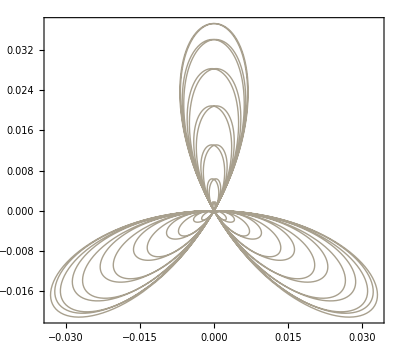

```mathematica
ParametricPlot[{Ex[t],Ey[t]},{t,0,2 π/modw},Frame->True,Axes->False,PlotRange->All,PlotStyle->{Thickness[0.0025]},ColorFunction->Function[{x,y,t},ColorData["DarkBands"][t]],ImageSize->Full]
```

```mathematica
Export["/Users/Dinosaur/Google Drive/Professional/website pics/pulsed_w-2w.png",%135,"PNG"]
```

/Users/Dinosaur/Google Drive/Professional/website pics/pulsed_w-2w.png

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

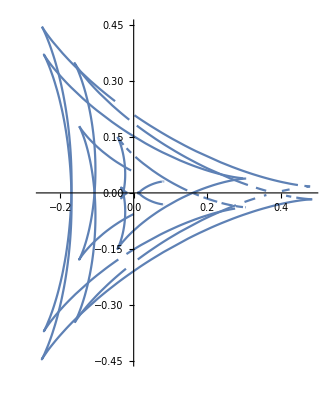

```mathematica
ParametricPlot[{A[t][[1]][[1]],A[t][[2]][[1]]},{t,0,2 π/modw}]
```

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

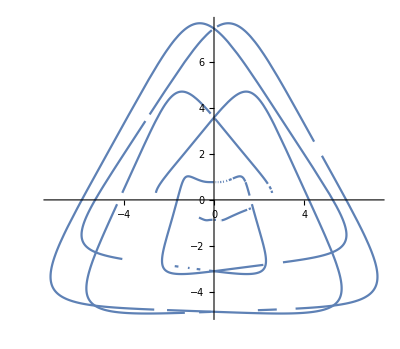

```mathematica
ParametricPlot[{alpha[t][[1]][[1]],alpha[t][[2]][[1]]},{t,0,2 π/modw}]
```

```mathematica
ParametricPlot3D[{big*alpha[t][[1]][[1]],big*alpha[t][[2]][[1]],t},{t,0,2 π/modw}]
```

```mathematica
big=500;
ParametricPlot3D[{t,big*Ex[t],big*Ey[t]},{t,0,2 π/modw}]
```

-Graphics3D-